```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\dodo\Desktop\triplet_nucleation\DB5C_5Csite\thermo

## For MultiWell/Thermo. Data from Lamm.

### Read Data and Preprocess

```mathematica
AllData=Import["scan.txt","Data"]
```

{{1,-145.,********,0.,37.475,0.4},{2,-135.,********,76.7,38.165,0.4},{3,-125.,********,278.8,38.881,0.4},{4,-115.,********,565.7,45.161,0.4},{5,-105.,********,855.8,59.581,0.3},{6,-95.,********,1058.6,81.316,0.2},{7,-85.,********,1079.2,81.927,0.2},{8,-75.,********,907.8,64.271,0.3},{9,-65.,********,623.3,51.097,0.3},{10,-55.,-0.959931,323.7,40.531,0.4},{11,-45.,-0.785398,100.1,35.127,0.5},{12,-35.,-0.610865,18.5,33.346,0.5},{13,-25.,-0.436332,104.2,33.988,0.5},{14,-15.,-0.261799,342.2,40.656,0.4},{15,-5.,-0.087266,670.3,120.37,0.1},{16,5.,0.087266,699.6,124.979,0.1},{17,15.,0.261799,373.,43.327,0.4},{18,25.,0.436332,116.9,33.847,0.5},{19,35.,0.610865,12.7,32.485,0.5},{20,45.,0.785398,78.3,34.27,0.5},{21,55.,0.959931,287.3,40.211,0.4},{22,65.,1.13446,579.9,48.474,0.3},{23,75.,1.309,875.6,63.333,0.3},{24,85.,1.48353,1062.8,83.263,0.2},{25,95.,1.65806,1066.9,78.43,0.2},{26,105.,1.8326,883.4,60.833,0.3},{27,115.,2.00713,605.,47.284,0.4},{28,125.,2.18166,316.1,39.719,0.4},{29,135.,2.35619,98.5,38.373,0.4},{30,145.,2.53073,10.9,39.224,0.4},{31,155.,2.70526,81.6,40.478,0.4},{32,165.,2.87979,303.1,42.358,0.4},{33,175.,3.05433,643.2,164.023,0.1},{34,185.,3.22886,680.1,173.974,0.1},{35,195.,3.40339,339.5,44.474,0.4},{36,205.,3.57793,96.1,25.496,0.7}}

```mathematica
NumData=Length[AllData⟦All,1⟧]
```

36

```mathematica
Angle[Unit_]:=If[Unit=="DEG",AllData⟦All,2⟧,If[Unit=="RAD",AllData⟦All,2⟧*2*π/360,Print["Unit = \"DEG\" or \"RAD\", not " ,Unit]]]
```

```mathematica
Energy[Unit_]:=If[Unit=="CM-1",AllData⟦All,4⟧,If[Unit=="KCAL",AllData⟦All,4⟧*0.002859,Print["Unit = \"CM-1\" or \"KCAL\""]]]
```

```mathematica
RotConRed[Unit_]:=If[Unit=="AMUA2",AllData⟦All,5⟧,If[Unit=="CM-1",16.86/AllData⟦All,5⟧,Print["Unit = \"CM-1\" or \"AMUA2\""]]]
```

```mathematica
EnergyData[AngUnit_,EneUnit_]:=Table[{Angle[AngUnit]⟦i⟧,Energy[EneUnit]⟦i⟧},{i,1,NumData}]
```

```mathematica
EnergyData["DEG","KCAL"]
```

{{-145.,0.},{-135.,0.219285},{-125.,0.797089},{-115.,1.61734},{-105.,2.44673},{-95.,3.02654},{-85.,3.08543},{-75.,2.5954},{-65.,1.78201},{-55.,0.925458},{-45.,0.286186},{-35.,0.0528915},{-25.,0.297908},{-15.,0.97835},{-5.,1.91639},{5.,2.00016},{15.,1.06641},{25.,0.334217},{35.,0.0363093},{45.,0.22386},{55.,0.821391},{65.,1.65793},{75.,2.50334},{85.,3.03855},{95.,3.05027},{105.,2.52564},{115.,1.7297},{125.,0.90373},{135.,0.281612},{145.,0.0311631},{155.,0.233294},{165.,0.866563},{175.,1.83891},{185.,1.94441},{195.,0.970631},{205.,0.27475}}

```mathematica
RotConData[AngUnit_,RotConUnit_]:=Table[{Angle[AngUnit]⟦i⟧,RotConRed[RotConUnit]⟦i⟧},{i,1,NumData}]
```

```mathematica
RotConData["DEG","AMUA2"]
```

{{-145.,37.475},{-135.,38.165},{-125.,38.881},{-115.,45.161},{-105.,59.581},{-95.,81.316},{-85.,81.927},{-75.,64.271},{-65.,51.097},{-55.,40.531},{-45.,35.127},{-35.,33.346},{-25.,33.988},{-15.,40.656},{-5.,120.37},{5.,124.979},{15.,43.327},{25.,33.847},{35.,32.485},{45.,34.27},{55.,40.211},{65.,48.474},{75.,63.333},{85.,83.263},{95.,78.43},{105.,60.833},{115.,47.284},{125.,39.719},{135.,38.373},{145.,39.224},{155.,40.478},{165.,42.358},{175.,164.023},{185.,173.974},{195.,44.474},{205.,25.496}}

### Plot and Interpolation

```mathematica
EnergyPlot[AngUnit_,EneUnit_]:=(plotframedGT={{Style["Energy ("<>EneUnit<>")",Italic,17],},{Style[" Diheral ("<>AngUnit<>")",Italic,17],}};
ListPlot[EnergyData[AngUnit,EneUnit],
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed},
                  PlotMarkers-> {Automatic,Medium}
                    ])
```

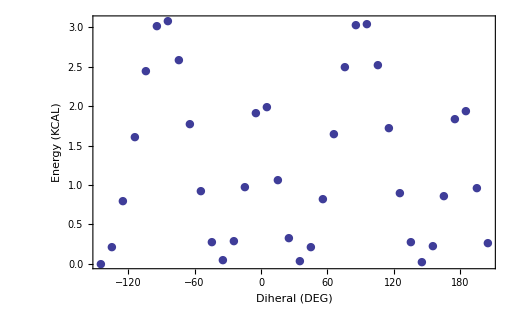

```mathematica
EnergyPlot["DEG","KCAL"]
```

```mathematica
EnergyFit[AngUnit_,EneUnit_]:=Interpolation[EnergyData[AngUnit,EneUnit]]
EnergyFitPlot[AngUnit_,EneUnit_]:=(plotframedGT={{Style["Energy ("<>EneUnit<>")",Italic,17],},{Style[" Diheral ("<>AngUnit<>")",Italic,17],}};
Plot[EnergyFit[AngUnit,EneUnit][x],{x,Min[Angle[AngUnit]],Max[Angle[AngUnit]]},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,PlotStyle-> Red,AxesStyle-> White
                    ])
```

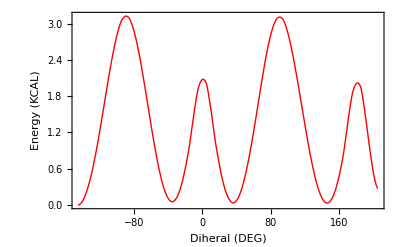

```mathematica
EnergyFitPlot["DEG","KCAL"]
```

```mathematica
RotConPlot[AngUnit_,RotConUnit_]:=(plotframedGT={{Style["Reduced Rotation Constant ("<>RotConUnit<>")",Italic,17],},{Style[" Diheral ("<>AngUnit<>")",Italic,17],}};
ListPlot[RotConData[AngUnit,RotConUnit],
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,PlotRange-> All,
                  AxesStyle->{White,Dashed},
                  PlotMarkers-> {Automatic,Medium}
                    ])
```

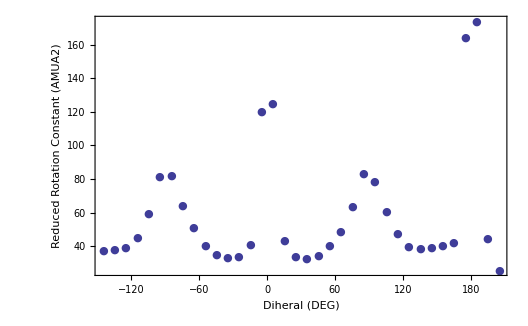

```mathematica
RotConPlot["DEG","AMUA2"]
```

```mathematica
RotConFit[AngUnit_,RotConUnit_]:=Interpolation[RotConData[AngUnit,RotConUnit]]
RotConFitPlot[AngUnit_,RotConUnit_]:=(plotframedGT={{Style["Reduced Rotation Constant ("<>RotConUnit<>")",Italic,17],},{Style[" Diheral ("<>AngUnit<>")",Italic,17],}};
Plot[RotConFit[AngUnit,RotConUnit][x],{x,Min[Angle[AngUnit]],Max[Angle[AngUnit]]},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,PlotRange-> All,
                  AspectRatio-> 1/GoldenRatio,PlotStyle-> Red,AxesStyle-> White
                    ])
```

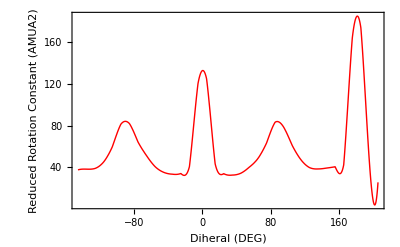

```mathematica
RotConFitPlot["DEG","AMUA2"]
```

### Shift to Angle \in [-180,180]

```mathematica
ShiftAngle=-180-Min[Angle["DEG"]](*-130*)(*Degree*)
```

-35.

```mathematica
onecircle[unit_]:=If[unit=="DEG",360,If[unit=="RAD",2*π]]
AngleUnit[shiftindegree_,unit_]:=If[unit=="DEG",shiftindegree,If[unit=="RAD",shiftindegree*2*π/360]]
```

```mathematica
(*EnergyShift[x_,shift_,AngUnit_,EneUnit_]:=If[(x-Min[Angle[AngUnit]])<=0&&(x-Min[Angle[AngUnit]])≥-ShiftAngleUnit[shift,AngUnit],EnergyShift[x]=EnergyFit[AngUnit,EneUnit][x+onecircle[AngUnit]],EnergyShift[x]=EnergyFit[AngUnit,EneUnit][x]]
EnergyShiftPlot[shift_,AngUnit_,EneUnit_]:=(plotframedGT={{Style["Energy ("<>EneUnit<>")",Italic,17],},{Style[" Diheral ("<>AngUnit<>")",Italic,17],}};
Plot[EnergyShift[x,shift,AngUnit,EneUnit],{x,Min[Angle[AngUnit]]+ShiftAngleUnit[shift,AngUnit],Max[Angle[AngUnit]]+ShiftAngleUnit[shift,AngUnit]},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,PlotStyle-> Red,AxesStyle-> White
                    ])*)
EnergyShift[x_,AngUnit_,EneUnit_]:=If[(x-Min[Angle[AngUnit]])<=0&&x≥AngleUnit[-180,AngUnit],EnergyShift[x]=EnergyFit[AngUnit,EneUnit][x+onecircle[AngUnit]],EnergyShift[x]=EnergyFit[AngUnit,EneUnit][x]]
EnergyShiftPlot[AngUnit_,EneUnit_]:=(plotframedGT={{Style["Energy ("<>EneUnit<>")",Italic,17],},{Style[" Diheral ("<>AngUnit<>")",Italic,17],}};
Plot[EnergyShift[x,AngUnit,EneUnit],{x,AngleUnit[-180,AngUnit],AngleUnit[180,AngUnit]},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,PlotStyle-> Red,AxesStyle-> White
                    ])
```

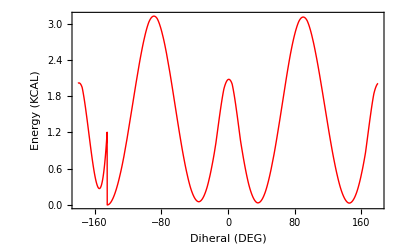

```mathematica
EnergyShiftPlot["DEG","KCAL"]
```

```mathematica
(*RotConShift[x_,shift_,AngUnit_,RotConUnit_]:=If[(x-Min[Angle[AngUnit]])<=0&&(x-Min[Angle[AngUnit]])>=ShiftAngleUnit[shift,AngUnit],RotConShift[x]=RotConFit[AngUnit,RotConUnit][x+onecircle[AngUnit]],RotConShift[x]=RotConFit[AngUnit,RotConUnit][x]]
RotConShiftPlot[shift_,AngUnit_,RotConUnit_]:=(plotframedGT={{Style["Reduced Rotation Constant ("<>RotConUnit<>")",Italic,17],},{Style[" Diheral ("<>AngUnit<>")",Italic,17],}};
Plot[RotConShift[x,shift,AngUnit,RotConUnit],{x,Min[Angle[AngUnit]]+ShiftAngleUnit[shift,AngUnit],Max[Angle[AngUnit]]+ShiftAngleUnit[shift,AngUnit]},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,PlotRange-> All,
                  AspectRatio-> 1/GoldenRatio,PlotStyle-> Red,AxesStyle-> White
                    ])*)
RotConShift[x_,AngUnit_,RotConUnit_]:=If[(x-Min[Angle[AngUnit]])<=0&&x>=AngleUnit[-180,AngUnit],RotConShift[x]=RotConFit[AngUnit,RotConUnit][x+onecircle[AngUnit]],RotConShift[x]=RotConFit[AngUnit,RotConUnit][x]]
RotConShiftPlot[AngUnit_,RotConUnit_]:=(plotframedGT={{Style["Reduced Rotation Constant ("<>RotConUnit<>")",Italic,17],},{Style[" Diheral ("<>AngUnit<>")",Italic,17],}};
Plot[RotConShift[x,AngUnit,RotConUnit],{x,AngleUnit[-180,AngUnit],AngleUnit[180,AngUnit]},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,PlotRange-> All,
                  AspectRatio-> 1/GoldenRatio,PlotStyle-> Red,AxesStyle-> White
                    ])
```

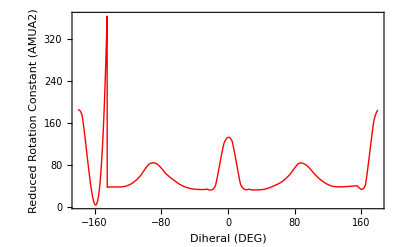

```mathematica
RotConShiftPlot["DEG","AMUA2"]
```

### Fitting by Fourier Series

```mathematica
FitFourier[funct_,trunc_,symmNum_,type_]:={(*symmNum is the symmetry number of potential, instead of the torsion*)
a0=1/(2*π)NIntegrate[funct,{x,-π,π},WorkingPrecision-> 10];
a[n_]:=1/π NIntegrate[funct*Cos[symmNum*n*x],{x,-π,π},WorkingPrecision-> 10];
b[n_]:=1/π NIntegrate[funct*Sin[symmNum*n*x],{x,-π,π},WorkingPrecision-> 10];
If[type=="COS+SIN",FitFunction[y_]:=a0+Sum[a[i]*Cos[symmNum*i*y],{i,trunc}]+Sum[b[i]*Sin[symmNum*i*y],{i,trunc}],If[type=="COSONLY",FitFunction[y_]:=a0+Sum[a[i]*Cos[symmNum*i*y],{i,trunc}]]];
FitFunction[x]}
```

```mathematica
symmNumenergy=2;
fittypeenergy="COSONLY";
energyfit=FitFourier[EnergyShift[x,"RAD","KCAL"],4,symmNumenergy,fittypeenergy]
```

{1.299008598-0.8005633863 Cos[2 x]+1.12258633 Cos[4 x]+0.1889450117 Cos[6 x]+0.127690474 Cos[8 x]}

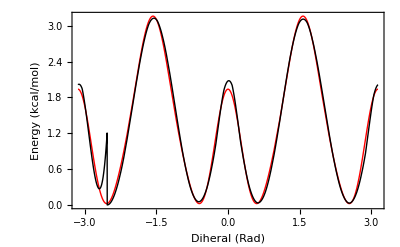

```mathematica
plotframedGT={{Style["Energy (kcal/mol)",Italic,17],},{Style[" Diheral (Rad)",Italic,17],}};
Plot[{energyfit,EnergyShift[x,"RAD","KCAL"]},{x,-π,π},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed},PlotStyle->{Red,Black}
               (*   PlotMarkers-> {Automatic,Medium*)
                    ]
```

```mathematica
symmNumrotcon=2;
fittyperotcon="COSONLY";
rotconfit=FitFourier[RotConShift[x,"RAD","AMUA2"],4,symmNumrotcon,fittyperotcon]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{61.44951763+10.44748426 Cos[2 x]+30.47239831 Cos[4 x]+9.558271932 Cos[6 x]+19.27802388 Cos[8 x]}

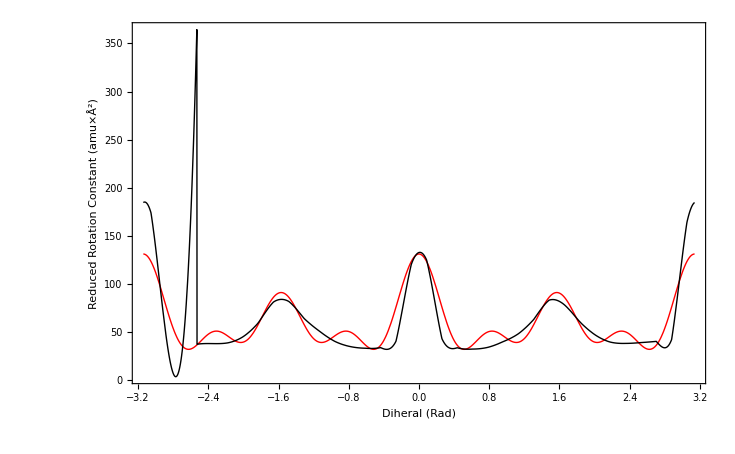

```mathematica
plotframedGT={{Style["Reduced Rotation Constant (amu×Å^2)",Italic,17],},{Style[" Diheral (Rad)",Italic,17],}};
Plot[{rotconfit,RotConShift[x,"RAD","AMUA2"]},{x,-π,π},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,PlotRange-> All,
                  AxesStyle->{White,Dashed},PlotStyle->{Red,Black}
               (*   PlotMarkers-> {Automatic,Medium*)
                    ]
```

### Final Results

```mathematica
Print[" Phase Angle:  ", ShiftAngle ,   "It doesn't matter to treat as 0 in hrd"]
Print[" Potential Type:  ", If[fittypeenergy=="COSONLY","Vhrd2","Vhrd3"]]
Print[" Symmetry number of potential: ", symmNumenergy]
Print[" Fitting Potential: ", energyfit]
Print[" Rotation Const Type:  Ihrd1" ]
Print[" Symmetry number of mass: ", symmNumrotcon]
Print[" Fitting rotation const: ", rotconfit]
If[symmNumenergy==symmNumrotcon,Print["Symmetry number of the hindered rotor: ", symmNumenergy]]
```

Phase Angle:  -35.It doesn't matter to treat as 0 in hrd

Potential Type:  Vhrd2

Symmetry number of potential: 2

Fitting Potential: {1.299008598-0.8005633863 Cos[2 x]+1.12258633 Cos[4 x]+0.1889450117 Cos[6 x]+0.127690474 Cos[8 x]}

Rotation Const Type:  Ihrd1

Symmetry number of mass: 2

Fitting rotation const: {61.44951763+10.44748426 Cos[2 x]+30.47239831 Cos[4 x]+9.558271932 Cos[6 x]+19.27802388 Cos[8 x]}

Symmetry number of the hindered rotor: 2

## Units

1 Bohr = 0.5291772083 Angstrom
1 Hartree = 27.21138505 eV
1 eV = 23.0605 kcal/mol = 96.4853 kJ/mol = 8065.54 cm-1
eV * nm = 1240
491K=1kcal/mol
1cm-1=0.002859kcal/mol
1kcal/mol=349.8cm-1
1 amuA^2=16.86/(1 cm^-1)